```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 169 Kb

{Utilities`CleanSlate`,CompiledFunctionTools`,IPOPTLink`,VariationalMethods`,Parallel`Debug`Perfmon`,Parallel`Debug`,System`,Global`}

```mathematica
Clear[q]
q = { r[t] , θ[t] }
```

{r[t],θ[t]}

```mathematica
Integrate[ (- k)/𝓇^2, {𝓇,∞,r} ]
```

ConditionalExpression[k/r, Im[r]≠0||Re[r]>0]

```mathematica
Clear[V]
V = 
(-1)* Assuming[
Im[r[t]]≠0||Re[r[t]]>0 ,
Integrate[ (- k)/𝓇^2, {𝓇,∞,r[t]} ] ]
```

-k/r[t]

```mathematica
Clear[s]
s = { r[t] Cos[θ[t]] , r[t] Sin[θ[t]] }
```

{Cos[θ[t]] r[t],r[t] Sin[θ[t]]}

```mathematica
D[s, t]
```

{Cos[θ[t]] r'[t]-r[t] Sin[θ[t]] θ'[t],Sin[θ[t]] r'[t]+Cos[θ[t]] r[t] θ'[t]}

```mathematica
D[s, t] . D[s, t]
```

(Sin[θ[t]] r'[t]+Cos[θ[t]] r[t] θ'[t])^2+(Cos[θ[t]] r'[t]-r[t] Sin[θ[t]] θ'[t])^2

```mathematica
D[s, t] . D[s, t] // Expand
```

Cos[θ[t]]^2 r'[t]^2+Sin[θ[t]]^2 r'[t]^2+Cos[θ[t]]^2 r[t]^2 θ'[t]^2+r[t]^2 Sin[θ[t]]^2 θ'[t]^2

```mathematica
D[s, t] . D[s, t] // Expand  // Simplify
```

r'[t]^2+r[t]^2 θ'[t]^2

```mathematica
Clear[T]
T = 1/2 m ( D[s, t] . D[s, t] // Expand  // Simplify  )
```

1/2 m (r'[t]^2+r[t]^2 θ'[t]^2)

```mathematica
Clear[ℒ]
ℒ = T - V
```

k/r[t]+1/2 m (r'[t]^2+r[t]^2 θ'[t]^2)

```mathematica
ℒ // pdConv
```

k/(r(t))+1/2 m ((r(t))^2 ((∂θ(t))/(∂t))^2+((∂r(t))/(∂t))^2)

```mathematica
D[ D[ ℒ , D[q[[1]], t] ],t ]  - D[ ℒ , q[[1]] ] 
D[ D[ ℒ , D[q[[2]], t] ],t ]  - D[ ℒ , q[[2]] ]
```

k/r[t]^2-m r[t] θ'[t]^2+m r''[t]

2 m r[t] r'[t] θ'[t]+m r[t]^2 θ''[t]

```mathematica
Table[
D[ D[ ℒ , D[q[[i]], t] ],t ]  - D[ ℒ , q[[i]] ] == 0 ,
{i,1,2} ] // TableForm
```

k/r[t]^2-m r[t] θ'[t]^2+m r''[t]==0
2 m r[t] r'[t] θ'[t]+m r[t]^2 θ''[t]==0

```mathematica
Clear[eqs]
eqs = 
EulerEquations[ ℒ , q , t ] ;
eqs // TableForm
```

-k/r[t]^2+m r[t] θ'[t]^2-m r''[t]==0
-m r[t] (2 r'[t] θ'[t]+r[t] θ''[t])==0

```mathematica
eqs // TableForm // pdConv
```

-k/(r(t))^2-m (∂^2 r(t))/(∂t^2)+m r(t) ((∂θ(t))/(∂t))^2==0
-m r(t) (r(t) (∂^2 θ(t))/(∂t^2)+2 (∂r(t))/(∂t) (∂θ(t))/(∂t))==0

```mathematica
Clear[com]
com = FirstIntegrals[ ℒ , q, t ]  ;
com // TableForm
```

FirstIntegral[θ]→-m r[t]^2 θ'[t]
FirstIntegral[t]→(-2 k+m r[t] r'[t]^2+m r[t]^3 θ'[t]^2)/(2 r[t])

```mathematica
Clear[ics]
ics = { 
r[0] == 2,
r'[0] == 3,
θ[0] == π / 4 ,
θ'[0] == 1
} ;
ics // TableForm
```

r[0]==2
r'[0]==3
θ[0]==π/4
θ'[0]==1

```mathematica
Clear[parameters]
parameters = {
m-> 5,
k-> 20
} ;
parameters // TableForm
```

m→5
k→20

```mathematica
eqs /. parameters // TableForm
```

-20/r[t]^2+5 r[t] θ'[t]^2-5 r''[t]==0
-5 r[t] (2 r'[t] θ'[t]+r[t] θ''[t])==0

```mathematica
Clear[solution]
solution[t_] = 
First[NDSolve[ Union[eqs /. parameters, ics ] , q, { t, 0, 10 } ]]
```

{r[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t]}

```mathematica
Plot[ Evaluate[ q/. solution[t] ], { t , 0, 10 } , PlotLabels-> { q[[1]] , q[[2]] }  ]
```

-Graphics-

```mathematica
?Plot
```

```mathematica
solution[t]
solution[t][[1]]
solution[t][[1,2]]
```

{r[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t]}

r[t]→InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

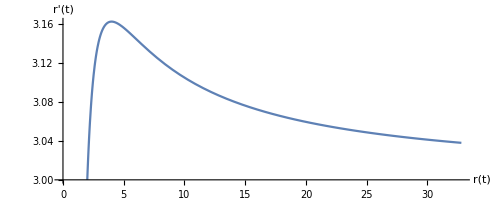

```mathematica
ParametricPlot[ { solution[t][[1,2]] , solution'[t][[1,2]] } , { t, 0 , 10 } , AxesLabel-> { q[[1]] , D[q[[1]], t] }  ]
```

```mathematica
solution[t]
solution[t][[2]]
solution[t][[2,2]]
```

{r[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t]}

θ[t]→InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

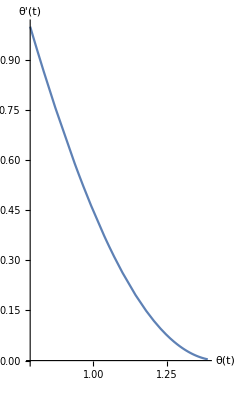

```mathematica
ParametricPlot[ { solution[t][[2,2]] , solution'[t][[2,2]] } , { t, 0 , 10 }  , PlotRange-> All, AxesLabel-> { q[[2]] , D[q[[2]], t] }]
```